### Understanding the rate of cargo transfer to Mars

Casey Handmer, September 2017

One of the more interesting problems of our time is sending humans to Mars and back. But any crewed Mars mission is only a precursor for the most exciting idea around - a self-sustaining city on Mars. 
I have written a bit about aspects of this problem, collated at caseyhandmer.com/home/mars. Here, for the first time, I present my calculations on how the cargo bandwidth may evolve over time. Understanding total mass capacity to Mars is important as importing Earth-built machines is the first step for bootstrapping a complete industrial stack on Mars. 
How much mass is necessary? Hard to say, but a million humans each with an average of 10x body weight in cargo is a million tonnes, so that seems like a good starting point. To put this in perspective, the largest container ships can transport about a quarter of this amount and offload and load completely in less than two days. The Berlin air lift moved 2.3 million tonnes of supplies in 15 months, with around 280,000 flights, in 1948-9. https://en.wikipedia.org/wiki/Berlin_Blockade
The underlying question, for which this provides a part of the answer, is: How to get to a self-sustaining Mars city as soon as possible?

#### Let’s get started

This is intended to be an idiomatic, complex model taking into account details such as multiple versions, multiple types, and ramps in production rate and reuse.

I downloaded launch window data from http://clowder.net/hop/railroad/EMa.htm .

```mathematica
launchwindowdata=ToExpression["{{"<>StringReplace["2001.2495\t3\t30\t2001\t2001.9582\t12\t15\t2001
2003.3849\t5\t19\t2003\t2004.0936\t2\t4\t2004
2005.5202\t7\t7\t2005\t2006.2290\t3\t22\t2006
2007.6556\t8\t26\t2007\t2008.3643\t5\t11\t2008
2009.7910\t10\t15\t2009\t2010.4997\t6\t30\t2010
2011.9264\t12\t4\t2011\t2012.6351\t8\t19\t2012
2014.0618\t1\t22\t2014\t2014.7705\t10\t7\t2014
2016.1972\t3\t11\t2016\t2016.9059\t11\t26\t2016
2018.3326\t4\t30\t2018\t2019.0413\t1\t15\t2019
2020.4679\t6\t18\t2020\t2021.1767\t3\t4\t2021
2022.6033\t8\t7\t2022\t2023.3120\t4\t22\t2023
2024.7387\t9\t26\t2024\t2025.4474\t6\t11\t2025
2026.8741\t11\t15\t2026\t2027.5828\t7\t30\t2027
2029.0095\t1\t3\t2029\t2029.7182\t9\t19\t2029
2031.1449\t2\t22\t2031\t2031.8536\t11\t7\t2031
2033.2803\t4\t11\t2033\t2033.9890\t12\t26\t2033
2035.4156\t5\t30\t2035\t2036.1244\t2\t15\t2036
2037.5510\t7\t18\t2037\t2038.2597\t4\t4\t2038
2039.6864\t9\t7\t2039\t2040.3951\t5\t22\t2040
2041.8218\t10\t26\t2041\t2042.5305\t7\t11\t2042
2043.9572\t12\t15\t2043\t2044.6659\t8\t30\t2044
2046.0926\t2\t3\t2046\t2046.8013\t10\t18\t2046
2048.2280\t3\t22\t2048\t2048.9367\t12\t7\t2048
2050.3633\t5\t11\t2050\t2051.0721\t1\t26\t2051
2052.4987\t6\t30\t2052\t2053.2074\t3\t15\t2053
2054.6341\t8\t18\t2054\t2055.3428\t5\t3\t2055
2056.7695\t10\t7\t2056\t2057.4782\t6\t22\t2057
2058.9049\t11\t26\t2058\t2059.6136\t8\t11\t2059
2061.0403\t1\t14\t2061\t2061.7490\t9\t30\t2061
2063.1756\t3\t3\t2063\t2063.8844\t11\t18\t2063
2065.3110\t4\t22\t2065\t2066.0198\t1\t7\t2066
2067.4464\t6\t11\t2067\t2068.1551\t2\t26\t2068
2069.5818\t7\t29\t2069\t2070.2905\t4\t15\t2070
2071.7172\t9\t18\t2071\t2072.4259\t6\t3\t2072
2073.8526\t11\t7\t2073\t2074.5613\t7\t22\t2074
2075.9880\t12\t26\t2075\t2076.6967\t9\t11\t2076
2078.1233\t2\t14\t2078\t2078.8321\t10\t30\t2078
2080.2587\t4\t3\t2080\t2080.9674\t12\t18\t2080
2082.3941\t5\t22\t2082\t2083.1028\t2\t7\t2083
2084.5295\t7\t11\t2084\t2085.2382\t3\t26\t2085
2086.6649\t8\t29\t2086\t2087.3736\t5\t14\t2087
2088.8003\t10\t18\t2088\t2089.5090\t7\t3\t2089
2090.9357\t12\t7\t2090\t2091.6444\t8\t22\t2091
2093.0710\t1\t26\t2093\t2093.7798\t10\t11\t2093
2095.2064\t3\t14\t2095\t2095.9151\t11\t29\t2095
2097.3418\t5\t3\t2097\t2098.0505\t1\t18\t2098
2099.4772\t6\t22\t2099\t2100.1859\t3\t7\t2100
2101.6126\t8\t11\t2101\t2102.3213\t4\t26\t2102
2103.7480\t9\t29\t2103\t2104.4567\t6\t14\t2104
2105.8834\t11\t18\t2105\t2106.5921\t8\t3\t2106
2108.0187\t1\t7\t2108\t2108.7275\t9\t22\t2108
2110.1541\t2\t25\t2110\t2110.8628\t11\t11\t2110
2112.2895\t4\t14\t2112\t2112.9982\t12\t29\t2112
2114.4249\t6\t3\t2114\t2115.1336\t2\t18\t2115
2116.5603\t7\t22\t2116\t2117.2690\t4\t7\t2117
2118.6957\t9\t10\t2118\t2119.4044\t5\t26\t2119
2120.8311\t10\t29\t2120\t2121.5398\t7\t14\t2121
2122.9664\t12\t18\t2122\t2123.6752\t9\t3\t2123
2125.1018\t2\t7\t2125\t2125.8105\t10\t22\t2125
2127.2372\t3\t25\t2127\t2127.9459\t12\t11\t2127
2129.3726\t5\t14\t2129\t2130.0813\t1\t29\t2130
2131.5080\t7\t3\t2131\t2132.2167\t3\t18\t2132
2133.6434\t8\t22\t2133\t2134.3521\t5\t7\t2134
2135.7788\t10\t10\t2135\t2136.4875\t6\t25\t2136
2137.9141\t11\t29\t2137\t2138.6229\t8\t14\t2138
2140.0495\t1\t18\t2140\t2140.7582\t10\t3\t2140
2142.1849\t3\t7\t2142\t2142.8936\t11\t22\t2142
2144.3203\t4\t25\t2144\t2145.0290\t1\t10\t2145
2146.4557\t6\t14\t2146\t2147.1644\t2\t29\t2147
2148.5911\t8\t3\t2148\t2149.2998\t4\t18\t2149
2150.7265\t9\t22\t2150\t2151.4352\t6\t7\t2151
2152.8618\t11\t10\t2152\t2153.5706\t7\t25\t2153
2154.9972\t12\t29\t2154\t2155.7059\t9\t14\t2155
2157.1326\t2\t18\t2157\t2157.8413\t11\t3\t2157
2159.2680\t4\t6\t2159\t2159.9767\t12\t22\t2159
2161.4034\t5\t25\t2161\t2162.1121\t2\t10\t2162
2163.5388\t7\t14\t2163\t2164.2475\t3\t29\t2164
2165.6742\t9\t3\t2165\t2166.3829\t5\t18\t2166
2167.8095\t10\t21\t2167\t2168.5183\t7\t7\t2168
2169.9449\t12\t10\t2169\t2170.6536\t8\t25\t2170
2172.0803\t1\t29\t2172\t2172.7890\t10\t14\t2172
2174.2157\t3\t18\t2174\t2174.9244\t12\t3\t2174
2176.3511\t5\t6\t2176\t2177.0598\t1\t22\t2177
2178.4865\t6\t25\t2178\t2179.1952\t3\t10\t2179
2180.6219\t8\t14\t2180\t2181.3306\t4\t29\t2181
2182.7572\t10\t3\t2182\t2183.4660\t6\t18\t2183
2184.8926\t11\t21\t2184\t2185.6013\t8\t6\t2185
2187.0280\t1\t10\t2187\t2187.7367\t9\t25\t2187
2189.1634\t2\t29\t2189\t2189.8721\t11\t14\t2189
2191.2988\t4\t18\t2191\t2192.0075\t1\t3\t2192
2193.4342\t6\t6\t2193\t2194.1429\t2\t21\t2194
2195.5695\t7\t25\t2195\t2196.2783\t4\t10\t2196
2197.7049\t9\t14\t2197\t2198.4136\t5\t29\t2198
2199.8403\t11\t3\t2199\t2200.5490\t7\t18\t2200
2201.9757\t12\t21\t2201\t2202.6844\t9\t6\t2202
2204.1111\t2\t10\t2204\t2204.8198\t10\t25\t2204
2206.2465\t3\t29\t2206\t2206.9552\t12\t14\t2206
2208.3819\t5\t17\t2208\t2209.0906\t2\t3\t2209
2210.5172\t7\t6\t2210\t2211.2260\t3\t21\t2211
2212.6526\t8\t25\t2212\t2213.3613\t5\t10\t2213
2214.7880\t10\t14\t2214\t2215.4967\t6\t29\t2215
2216.9234\t12\t2\t2216\t2217.6321\t8\t18\t2217
2219.0588\t1\t21\t2219\t2219.7675\t10\t6\t2219
2221.1942\t3\t10\t2221\t2221.9029\t11\t25\t2221
2223.3296\t4\t29\t2223\t2224.0383\t1\t14\t2224
2225.4649\t6\t17\t2225\t2226.1737\t3\t3\t2226
2227.6003\t8\t6\t2227\t2228.3090\t4\t21\t2228
2229.7357\t9\t25\t2229\t2230.4444\t6\t10\t2230
2231.8711\t11\t14\t2231\t2232.5798\t7\t29\t2232
2234.0065\t1\t2\t2234\t2234.7152\t9\t17\t2234
2236.1419\t2\t21\t2236\t2236.8506\t11\t6\t2236
2238.2773\t4\t10\t2238\t2238.9860\t12\t25\t2238
2240.4126\t5\t29\t2240\t2241.1214\t2\t14\t2241
2242.5480\t7\t17\t2242\t2243.2567\t4\t2\t2243
2244.6834\t9\t6\t2244\t2245.3921\t5\t21\t2245
2246.8188\t10\t25\t2246\t2247.5275\t7\t10\t2247
2248.9542\t12\t14\t2248\t2249.6629\t8\t29\t2249
2251.0896\t2\t2\t2251\t2251.7983\t10\t17\t2251
2253.2250\t3\t21\t2253\t2253.9337\t12\t6\t2253
2255.3603\t5\t10\t2255\t2256.0691\t1\t25\t2256
2257.4957\t6\t28\t2257\t2258.2044\t3\t14\t2258
2259.6311\t8\t17\t2259\t2260.3398\t5\t2\t2260
2261.7665\t10\t6\t2261\t2262.4752\t6\t21\t2262
2263.9019\t11\t25\t2263\t2264.6106\t8\t10\t2264
2266.0373\t1\t13\t2266\t2266.7460\t9\t29\t2266
2268.1727\t3\t2\t2268\t2268.8814\t11\t17\t2268
2270.3080\t4\t21\t2270\t2271.0168\t1\t6\t2271
2272.4434\t6\t10\t2272\t2273.1521\t2\t25\t2273
2274.5788\t7\t28\t2274\t2275.2875\t4\t14\t2275
2276.7142\t9\t17\t2276\t2277.4229\t6\t2\t2277
2278.8496\t11\t6\t2278\t2279.5583\t7\t21\t2279
2280.9850\t12\t25\t2280\t2281.6937\t9\t10\t2281
2283.1204\t2\t13\t2283\t2283.8291\t10\t28\t2283
2285.2557\t4\t2\t2285\t2285.9645\t12\t17\t2285
2287.3911\t5\t21\t2287\t2288.0998\t2\t6\t2288
2289.5265\t7\t10\t2289\t2290.2352\t3\t25\t2290
2291.6619\t8\t28\t2291\t2292.3706\t5\t13\t2292
2293.7973\t10\t17\t2293\t2294.5060\t7\t2\t2294
2295.9327\t12\t6\t2295\t2296.6414\t8\t21\t2296
2298.0681\t1\t24\t2298\t2298.7768\t10\t10\t2298
2300.2034\t3\t13\t2300\t2300.9122\t11\t28\t2300
2302.3388\t5\t2\t2302\t2303.0475\t1\t17\t2303
2304.4742\t6\t21\t2304\t2305.1829\t3\t6\t2305
2306.6096\t8\t9\t2306\t2307.3183\t4\t25\t2307
2308.7450\t9\t28\t2308\t2309.4537\t6\t13\t2309
2310.8804\t11\t17\t2310\t2311.5891\t8\t2\t2311
2313.0157\t1\t6\t2313\t2313.7245\t9\t21\t2313",{"\t"->",","\n"->"},{"}]<>"}}"];
launchwindows=launchwindowdata[[All,1]]
```

{2001.25,2003.38,2005.52,2007.66,2009.79,2011.93,2014.06,2016.2,2018.33,2020.47,2022.6,2024.74,2026.87,2029.01,2031.14,2033.28,2035.42,2037.55,2039.69,2041.82,2043.96,2046.09,2048.23,2050.36,2052.5,2054.63,2056.77,2058.9,2061.04,2063.18,2065.31,2067.45,2069.58,2071.72,2073.85,2075.99,2078.12,2080.26,2082.39,2084.53,2086.66,2088.8,2090.94,2093.07,2095.21,2097.34,2099.48,2101.61,2103.75,2105.88,2108.02,2110.15,2112.29,2114.42,2116.56,2118.7,2120.83,2122.97,2125.1,2127.24,2129.37,2131.51,2133.64,2135.78,2137.91,2140.05,2142.18,2144.32,2146.46,2148.59,2150.73,2152.86,2155.,2157.13,2159.27,2161.4,2163.54,2165.67,2167.81,2169.94,2172.08,2174.22,2176.35,2178.49,2180.62,2182.76,2184.89,2187.03,2189.16,2191.3,2193.43,2195.57,2197.7,2199.84,2201.98,2204.11,2206.25,2208.38,2210.52,2212.65,2214.79,2216.92,2219.06,2221.19,2223.33,2225.46,2227.6,2229.74,2231.87,2234.01,2236.14,2238.28,2240.41,2242.55,2244.68,2246.82,2248.95,2251.09,2253.23,2255.36,2257.5,2259.63,2261.77,2263.9,2266.04,2268.17,2270.31,2272.44,2274.58,2276.71,2278.85,2280.99,2283.12,2285.26,2287.39,2289.53,2291.66,2293.8,2295.93,2298.07,2300.2,2302.34,2304.47,2306.61,2308.75,2310.88,2313.02}

This array contains hypothesized types. Three one-off development vehicles, then a ~300T (payload to surface) starter model, followed by a ~1000T spaceship which pushes the limits, as I understand them, of how much mass can be aerodynamically navigated through the Martian atmosphere. Note that there are no warp drives or other exotics. They would be nice, but they are not necessary. This schema has first boots on the ground in 2030. It is not impossible to imagine earlier landings, but I’m trying to strike a balance here between hopeful and defensible. 

Type number, version, purpose, capacity to Mars (T), first launched, number of uses

```mathematica
types={
{"A","0.1","Atmospheric testing",0,2019,1},
{"B","0.2","Earth orbital testing",0,2019,1},
{"C","0.3","Mars landing",300,2022,1},
{"1","1.0","Mars landing and return test",100,2024,1},
{"?","1.1","Mars landing, ERV",200,2026,1},
{"?","1.2","First crew landing",200,2029,2},
{"?","1.3","Crew landing",300,2031,4},
{"?","1.4","Crew landing",330,2033,8},
{"?","1.5","Crew landing",340,2035,16},
{"?","2.0","Crew landing",800,2033,1},
{"?","2.1","Crew landing",900,2035,1},
{"?","2.2","Crew landing",900,2037,2},
{"?","2.3","Crew landing",1000,2039,6},
{"?","2.4","Crew landing",1100,2041,12},
{"?","2.5","Crew landing",1140,2043,30}};
```

```mathematica
Join[{{"Version","Purpose","Payload (T)","Uses"}},types[[All,{2,3,4,6}]]]//MatrixForm
```

(Version | Purpose | Payload (T) | Uses
0.1 | Atmospheric testing | 0 | 1
0.2 | Earth orbital testing | 0 | 1
0.3 | Mars landing | 300 | 1
1.0 | Mars landing and return test | 100 | 1
1.1 | Mars landing, ERV | 200 | 1
1.2 | First crew landing | 200 | 2
1.3 | Crew landing | 300 | 4
1.4 | Crew landing | 330 | 8
1.5 | Crew landing | 340 | 16
2.0 | Crew landing | 800 | 1
2.1 | Crew landing | 900 | 1
2.2 | Crew landing | 900 | 2
2.3 | Crew landing | 1000 | 6
2.4 | Crew landing | 1100 | 12
2.5 | Crew landing | 1140 | 30)

#### Model methodology

This model begins with a specified construction rate, which can be freely defined, then produces a series of dependent data structures.

#### Specify construction rate.

Each type has a start date, then steps through 6 versions, one per launch window, until final version achieved and rate increases. 
The build rate model is augmented logistic. This means that there’s an initial exponential(ish) ramp towards design rate, then a slower increase as additional construction efficiencies are integrated into the primary production line. 
These production rates, which sit at around 10 hulls per year, are not particularly crazy. Boeing will produce 14 787s per month in 2018, so we don’t need any miracles. The production rate encapsulates the full three-vehicle set: booster, tanker, ship. For any given flight of the ship, the booster and tanker will fly around 20 times.

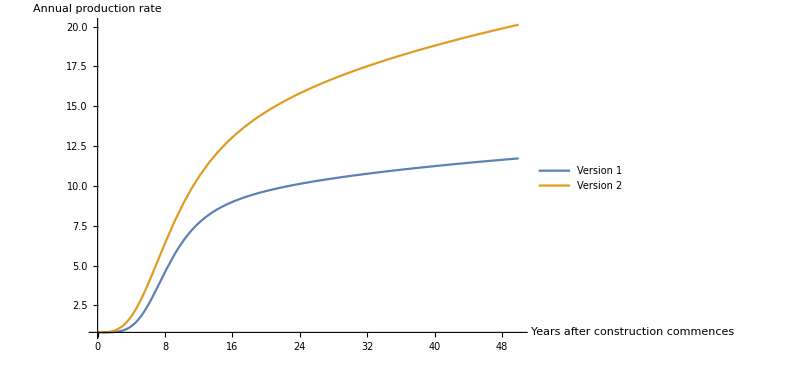

```mathematica
rate1=0.8+5t^4.2/(8^4+t^4);
rate2=0.8+6t^3.3/(8^3+t^3);
Plot[{rate1,rate2},{t,0,50},PlotRange->All,AxesStyle->16,AxesLabel->{"Years after \nconstruction \ncommences","Annual production rate"},ImageSize->600,PlotLegends->Placed[{"Version 1","Version 2"},Below]]
```

These functions takes a rate function and a start date, and produces a number of hulls of a given type built between given launch windows.

```mathematica
RateToHulls[rate_,startdate_]:=Transpose[{#,Chop[Table[NIntegrate[rate,{t,0,t2}],{t2,#-startdate}]]}]&[Select[launchwindows,#>startdate&]];
HullsToLaunches[hulls_]:=Select[Transpose[{hulls[[All,1]],Join[{Floor[hulls[[1,2]]]},Floor[hulls[[2;;-1,2]]-Floor[hulls[[1;;-2,2]]]]]}],#[[2]]>0&];
```

```mathematica
hullslaunchedatdate1=HullsToLaunches[RateToHulls[rate1,2022]];
hullslaunchedatdate2=HullsToLaunches[RateToHulls[rate2,2032]];
hullslaunchedatdate={hullslaunchedatdate1,hullslaunchedatdate2};
```

This function is a hacky mess which needs to be fixed, but it takes the list of the number of hulls completed since the last launch window, and integrates them into a common data set called “construction”. This data set is formatted:
{launch window year, type, array of {hull number, number of reuses}}
And forms a look up table by year and type.

```mathematica
veroffset=Table[0,Length[hullslaunchedatdate]];
construction={
{2019,"0.1",{{"A",0}}},
{2019,"0.2",{{"B",0}}},
{2022,"0.3",{{"C",1}}}};
Do[
Do[
type=If[j-veroffset[[k]]<Length[#],#[[j-veroffset[[k]]]],#[[-1]]]&[Select[types,Floor[ToExpression[#[[2]]]]==k&]];
hullnumberoffset=If[j==1&&k==1,0,#]&[construction[[-1,3,-1,1]]];
If[k>1&&Floor[hullslaunchedatdate[[k]][[j-veroffset[[k]],1]]]!=construction[[-1,1]],
veroffset[[k]]+=1;,construction=Join[construction,{{Floor[#[[1]]],type[[2]],Table[{hullnumberoffset+i,type[[6]]},{i,1,#[[2]]}]}&[hullslaunchedatdate[[k]][[j-veroffset[[k]]]]]}];];
,{k,1,Length[veroffset]}]
,{j,1,30}]
```

We’ve only computed the first 30 launch windows of production, but even more speculative future prediction can extend this up to Length[hullslaunchedatdate1].

This procedure constructs the global manifest. It is a long sorted list containing {year, hull number, version, tonnes to Mars} for all of the ships specified in construction. As a result, for years when existing hulls are being reused but no new hulls have yet been included, it may give incomplete results, which are chopped in this analysis.

```mathematica
globalmanifest=Sort[Flatten[Table[Table[Table[{Select[Floor[launchwindows],#≥construction[[k,1]]&][[i]],construction[[k,3,j,1]],construction[[k,2]],Select[types,#[[2]]==construction[[k,2]]&][[1,4]]},{i,1,construction[[k,3,j,2]]}],{j,1,Length[construction[[k,3]]]}],{k,1,Length[construction]}],2]];
```

Take time slice

The Select function in Mathematica will allow the globalmanifest to be used as a database to search by year, type, hull numbers, or mass consignment. This example shows all the flights that occurred in the 2029 launch window.

```mathematica
Select[globalmanifest,#[[1]]==Floor[launchwindows[[14]]]&]
```

{{2029,5,1.2,200},{2029,6,1.2,200},{2029,7,1.2,200},{2029,8,1.2,200},{2029,9,1.2,200},{2029,10,1.2,200}}

Adding all the masses from the previous example allows the construction of this graph, which shows the total mass sent each launch window.

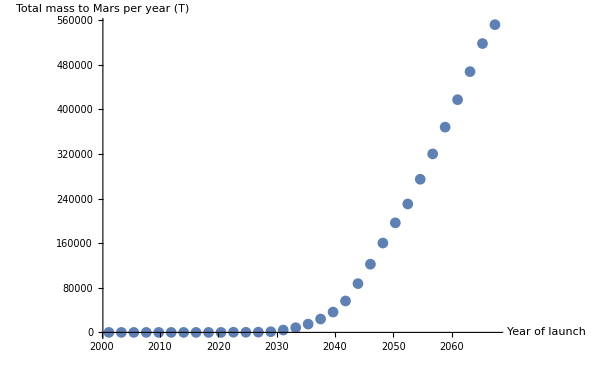

```mathematica
ListPlot[Table[{launchwindows[[i]],Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]]},{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}],AxesStyle->16,AxesLabel->{"Year of launch","Total mass to Mars per year (T)"},ImageSize->600,PlotRange->All]
```

This graph cumulative mass sent, broken down by type. So we see that within a decade of its introduction, the type 2 spaceship is sending most of the cargo. We also see that the target mass of a million tonnes is achieved during the 2052 launch window, which is only 24 years after the first boots on the ground.

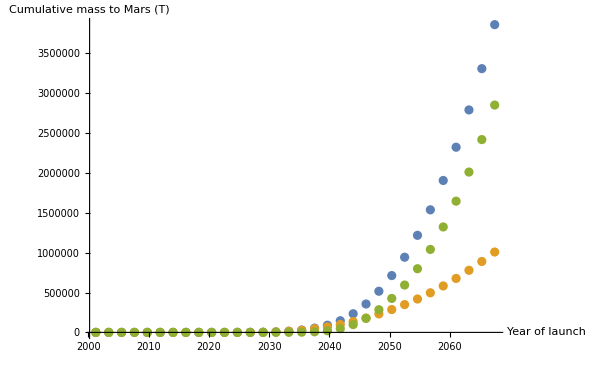

```mathematica
ListPlot[{Transpose[{launchwindows[[1;;Length[#]]],#}]&[Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]]},AxesStyle->16,AxesLabel->{"Year of launch","Cumulative mass to Mars (T)"},ImageSize->600,PlotRange->All]
```

These graphs are as above, but with vertical logarithmic scales to capture the complete history. Despite appearances, launch capacity is not growing exponentially. But quadratically is still pretty good!

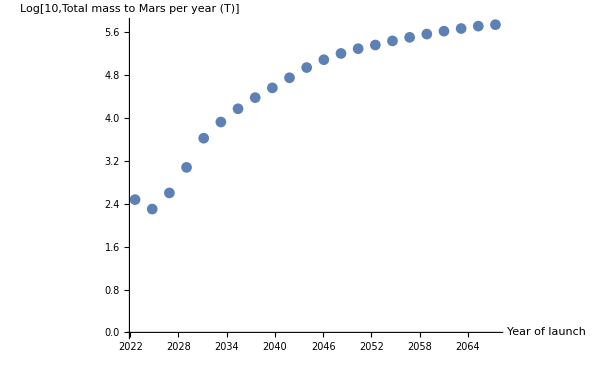

```mathematica
ListPlot[Table[{launchwindows[[i]],Log[10,Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]]]},{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}],AxesStyle->16,AxesLabel->{"Year of launch","Log[10,Total mass to Mars per year (T)]"},ImageSize->600,PlotRange->All]
```

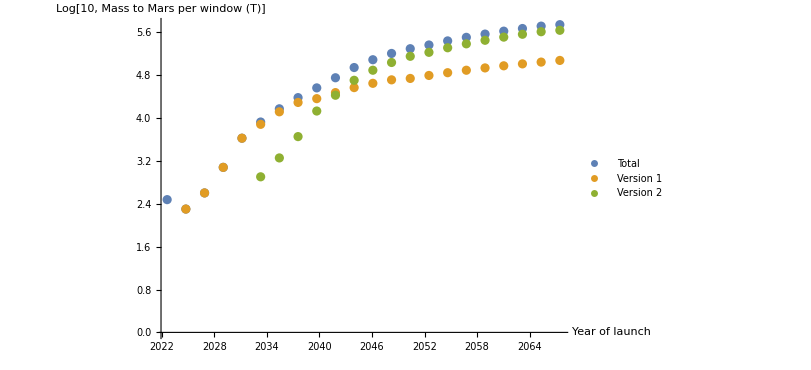

```mathematica
ListPlot[{Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]]},AxesStyle->16,AxesLabel->{"Year of launch","Log[10, Mass to Mars \nper window (T)]"},ImageSize->600,PlotRange->All,PlotLegends->Placed[{"Total","Version 1", "Version 2"},Below]]
```

This graph shows cumulative mass in log scale. Within a decade of type 2 development beginning, it lifts the overall mass envelope by about a factor of four, which is enough to hasten the million tonne milestone by 15 years, a reduction of nearly 40%. Of course, this is not enough to prove that, eg, increasing the rate of version 1 production by a factor of 4 wouldn’t be a better strategy! This doesn’t give us strong information on cost of development.

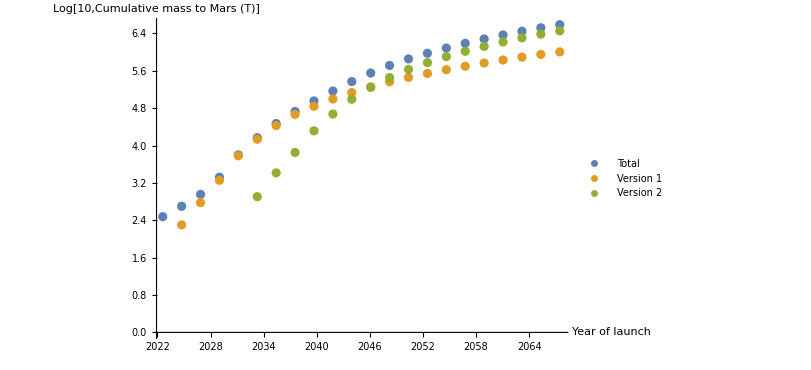

```mathematica
ListPlot[{Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Log[10,Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]]]},AxesStyle->16,AxesLabel->{"Year of launch","Log[10,Cumulative \nmass to Mars (T)]"},ImageSize->600,PlotRange->All,PlotLegends->Placed[{"Total","Version 1","Version 2"},Below]]
```

#### Construction rate

Here we reconstruction the construction rate from the construction array. This serves mainly to validate our original code. For context, Boeing’s 787 construction rate will hit 14/month in 2018.

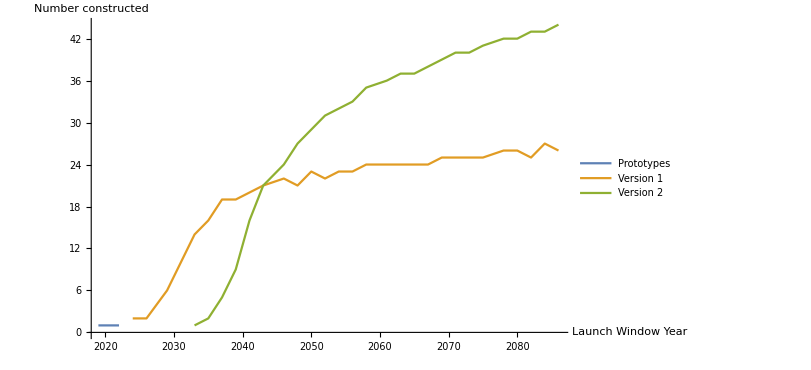

```mathematica
ListLinePlot[{Table[{#[[i,1]],Length[#[[i,3]]]},{i,1,Length[#]}]&[Select[construction,Floor[ToExpression[#[[2]]]]==0&]],Table[{#[[i,1]],Length[#[[i,3]]]},{i,1,Length[#]}]&[Select[construction,Floor[ToExpression[#[[2]]]]==1&]],Table[{#[[i,1]],Length[#[[i,3]]]},{i,1,Length[#]}]&[Select[construction,Floor[ToExpression[#[[2]]]]==2&]]},AxesStyle->16,AxesLabel->{"Launch Window Year","Number constructed"},ImageSize->600,PlotLegends->Placed[{"Prototypes","Version 1","Version 2"},Below]]
```

This graph shows the number of launches per window. Each of these launches implies about 20 tanker launches, so that implies about 8 launches from the ground per day if evenly spaced throughout the launch window. I don’t think this is a constraining factor.

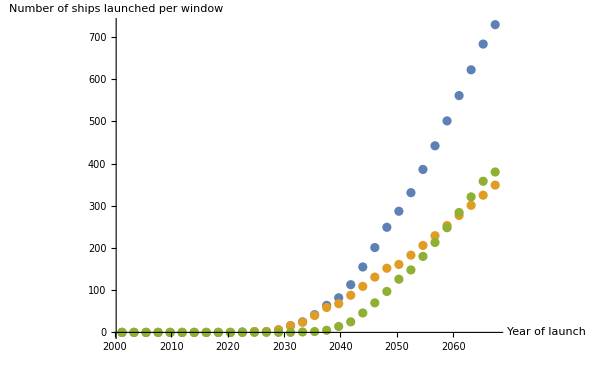

```mathematica
ListPlot[{Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]},AxesStyle->16,AxesLabel->{"Year of launch","Number of ships launched per window"},ImageSize->600,PlotRange->All]
```

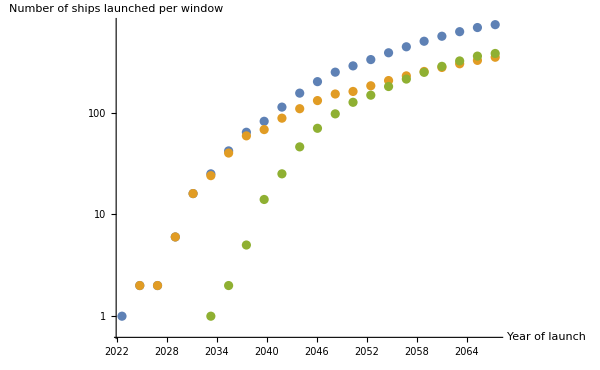

```mathematica
ListLogPlot[{Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]},AxesStyle->16,AxesLabel->{"Year of launch","Number of ships launched per window"},ImageSize->600,PlotRange->All]
```

Construct hull-specific histories

Here we can recover from the global manifest the history of a particular hull. Here, hull 15 was a type 1.3 that flew 4 missions in the 2030s. The assumption on reuse is that the Mars fuel/ox factory is up and running soon enough that all these ships can fly back during the same launch window, and thus fly once per launch window. It is possible to envision a version 3 spaceship with similar size to version 2 but bigger engines that can do trips per launch window, but is it necessary?

```mathematica
Select[globalmanifest,#[[2]]==15&]
```

{{2031,15,1.3,300},{2033,15,1.3,300},{2035,15,1.3,300},{2037,15,1.3,300}}

This graph shows the complete history of every hull specified in the global manifest. The vertical axis captures the sequential hull number, while the line parallel to the horizontal axis illustrates the ships career from first flight through retirement. For any given year, a vertical line crosses every ship active that year. Note that a million tonnes of cargo, cumulative, is reached in 2052, which is far to the bottom left.

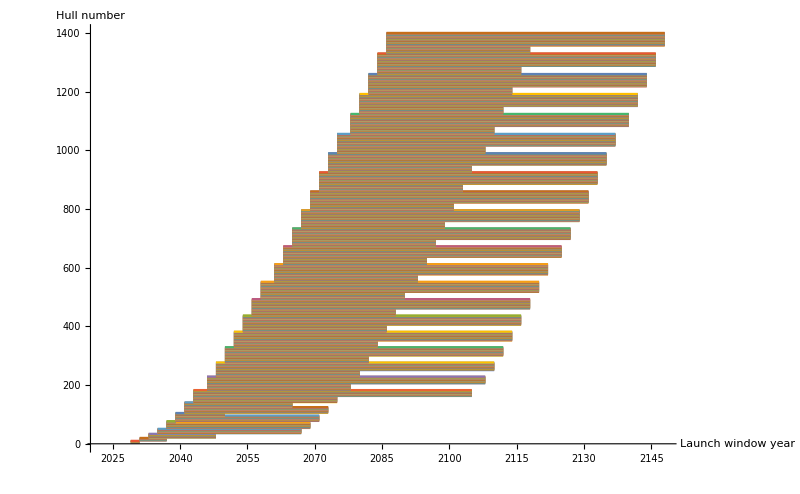

```mathematica
allhulls=DeleteDuplicates[globalmanifest[[All,2]]];
hullmanifests=Table[Select[globalmanifest,#[[2]]==allhulls[[i]]&],{i,1,Length[allhulls]}];
hullmanifests[[1,1,2]]=0;
ListLinePlot[hullmanifests[[All,All,{1,2}]],AxesStyle->16,AxesLabel->{"Launch window year","Hull number"},ImageSize->800]
```

#### How much mass is needed per human?

Assuming that each human results in a proportionate increase in mass self sufficiency, this relation is completely determined by the initial human/cargo ratio. Let’s set it so that the first 10 people landing in 2027 consume 900T of cargo then available, and eventually trend to personal cargo/food/body weight of 500kg.

This is the autarky trajectory given by the red line in the population scaling graph.

```mathematica
autarkytrajectory=Table[{10^y,0.5+3.94 885 10^(-(a b-b y+√(a c y-c y^2))/(a-y))}/.{a->7.8,b->1,c->6.1},{y,0,6.95,0.05}];
intauttraj=Interpolation[autarkytrajectory];
MassPopAutarky[pop_]:=intauttraj[pop];
```

Mass per person vs population.

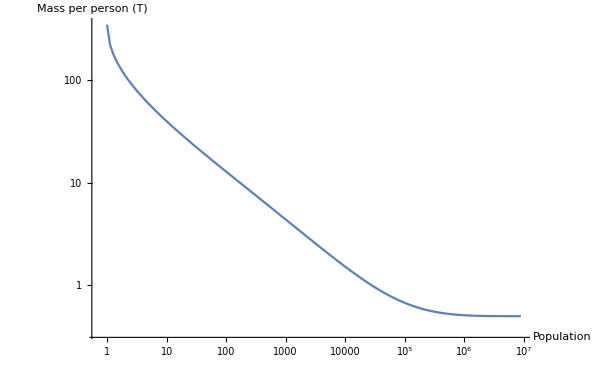

```mathematica
ListLogLogPlot[autarkytrajectory,PlotRange->All,Joined->True,AxesStyle->16,AxesLabel->{"Population","Mass per person (T)"},ImageSize->600]
```

```mathematica
masspopautarky=Table[{pop,MassPopAutarky[pop]},{pop,1,10^6.95,1}];
```

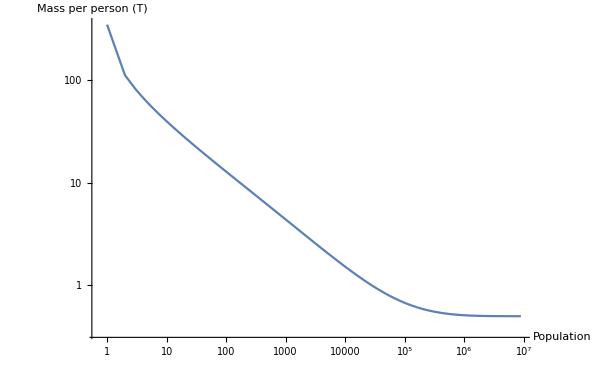

```mathematica
ListLogLogPlot[masspopautarky[[DeleteDuplicates[Table[Round[10^i],{i,0,6.95,0.05}]]]],PlotRange->All,Joined->True,AxesStyle->16,AxesLabel->{"Population","Mass per person (T)"},ImageSize->600]
```

Cumulative mass vs population.

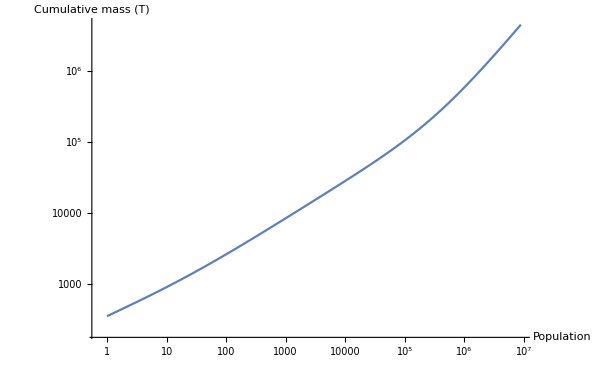

```mathematica
ListLogLogPlot[Transpose[{masspopautarky[[All,1]],Accumulate[masspopautarky[[All,2]]]}][[DeleteDuplicates[Table[Round[10^i],{i,0,6.95,0.05}]]]],AxesStyle->16,AxesLabel->{"Population","Cumulative mass (T)"},ImageSize->600,Joined->True]
```

```mathematica
intpopmassautarky=Interpolation[Transpose[{Accumulate[masspopautarky[[All,2]]],masspopautarky[[All,1]]}]];
PopMassAutarky[mass_]:=intpopmassautarky[mass];
```

```mathematica
massyear=Transpose[{launchwindows[[1;;Length[#]]],#}]&[Accumulate[Table[Total[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]]];
intmassyear=Interpolation[massyear];
MassYear[year_]:=intmassyear[year];
```

Combine the two and get population as a function of time.

```mathematica
Table[{year,Round[PopMassAutarky[MassYear[year]]]},{year,launchwindows[[13;;28]]}]
```

{{2026.87,10},{2029.01,64},{2031.14,570},{2033.28,2903},{2035.42,10825},{2037.55,31914},{2039.69,77012},{2041.82,163404},{2043.96,315447},{2046.09,542979},{2048.23,851510},{2050.36,1236554},{2052.5,1691991},{2054.63,2237720},{2056.77,2875524},{2058.9,3610258}}

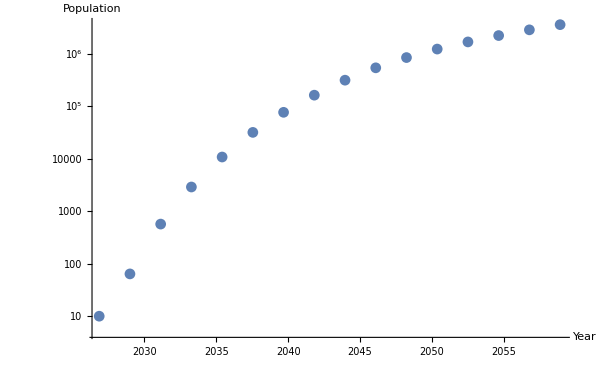

```mathematica
ListLogPlot[Table[{year,Round[PopMassAutarky[MassYear[year]]]},{year,launchwindows[[13;;28]]}],AxesStyle->16,AxesLabel->{"Year","Population"},ImageSize->600]
```

Year over year population increases. Early settlers will be mainly building more base!

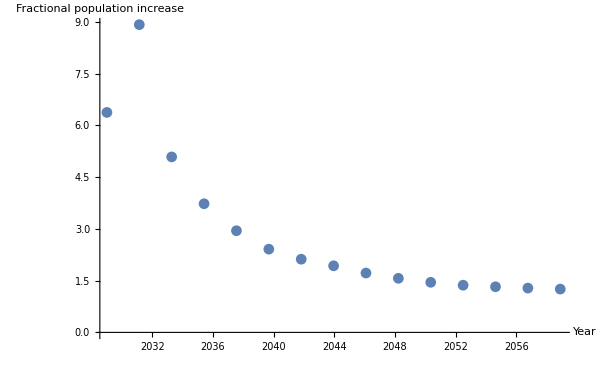

```mathematica
ListPlot[Transpose[{launchwindows[[14;;28]],#[[2;;-1]]/#[[1;;-2]]&[Table[PopMassAutarky[MassYear[year]],{year,launchwindows[[13;;28]]}]]}],PlotRange->All,AxesStyle->16,AxesLabel->{"Year","Fractional \npopulation \nincrease"},ImageSize->600]
```

Population increases vs population. After 2045, the bottleneck is shipping capacity.

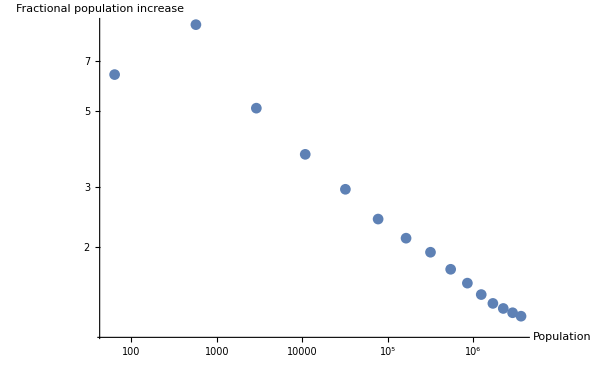

```mathematica
ListLogLogPlot[Transpose[{#[[2;;-1]],#[[2;;-1]]/#[[1;;-2]]}]&[Table[PopMassAutarky[MassYear[year]],{year,launchwindows[[13;;28]]}]],PlotRange->All,AxesStyle->16,AxesLabel->{"Population","Fractional \npopulation \nincrease"},ImageSize->600]
```

#### How much does it cost?

The basic idea here is to model the cost of building each ship, overhauling each ship, and launching each ship. Then assess revenue from people flying there and see what the net investment needs to be.

This is the number of people who fly each window.

```mathematica
Join[{10},Differences[Round[Table[PopMassAutarky[MassYear[year]],{year,launchwindows[[13;;28]]}]]]]
```

{10,54,506,2333,7922,21089,45098,86392,152043,227532,308531,385044,455437,545729,637804,734734}

It is very difficult to estimate development and initial production costs, except to guess, for instance, that it will take a combined work force of 50000 people each costing $100000/year for a total cost of around $5b/year. But the ramp will take a while to get near this.

Let’s see if we can formalize this by looking at total cargo vs number of people flown and total system costs.

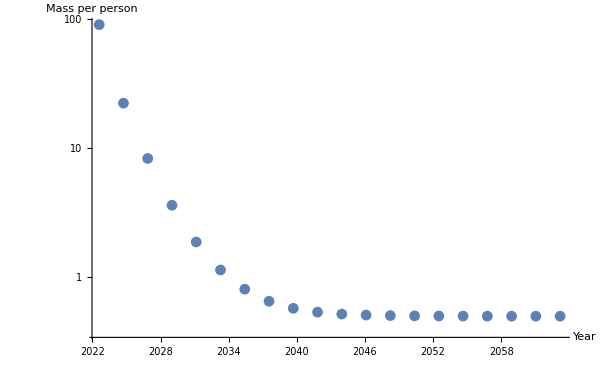

```mathematica
ListLogPlot[Transpose[{launchwindows[[11;;30]],N[Join[{900},Differences[massyear[[All,2]]][[13;;-1]]]/Join[{10},Differences[Round[Table[PopMassAutarky[MassYear[year]],{year,launchwindows[[13;;32]]}]]]]]}],PlotRange->All,AxesStyle->16,AxesLabel->{"Year","Mass per person"},ImageSize->600]
```

At some point (mid 2030s), however, production costs on Version 1 will likely fall to a level comparable to advanced composites jet aircraft or even slightly less, say $500m/booster+tanker+ship, with ongoing refitting costs of say $100m/launch window. Then, given 16 total uses, the cost will fall to an average of $125m/flight. If each ship takes 300 people, each with a tonne of cargo, the ticket price is $430000/ticket.

Later (mid 2040s), Version 2 can move 2000 people each with half a tonne of cargo, will fly 30 times with a refit cost of $50m and construction cost of $500m, reducing per ticket cost to around $35000.

By 2033, 38 ships will have already been constructed over 16 years. At a per ship cost of $500m, expenditure will exceed $10b.

```mathematica
buildratedata={Select[Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],#[[2]]>0&],Select[Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==1&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],#[[2]]>0&],Select[Transpose[{launchwindows[[1;;Length[#]]],#}]&[Table[Length[Select[globalmanifest,#[[1]]==Floor[launchwindows][[i]]&&Floor[ToExpression[#[[3]]]]==2&][[All,-1]]],{i,1,Length[DeleteDuplicates[construction[[All,1]]]]}]],#[[2]]>0&],Transpose[{launchwindows[[12;;32]],Select[Table[{construction[[i,1]],construction[[i,2]],Length[construction[[i,3]]]},{i,1,41}],Floor[ToExpression[#[[2]]]]==1&][[All,3]]}],Transpose[{launchwindows[[16;;32]],Select[Table[{construction[[i,1]],construction[[i,2]],Length[construction[[i,3]]]},{i,1,41}],Floor[ToExpression[#[[2]]]]==2&][[All,{1,3}]]}]};
```

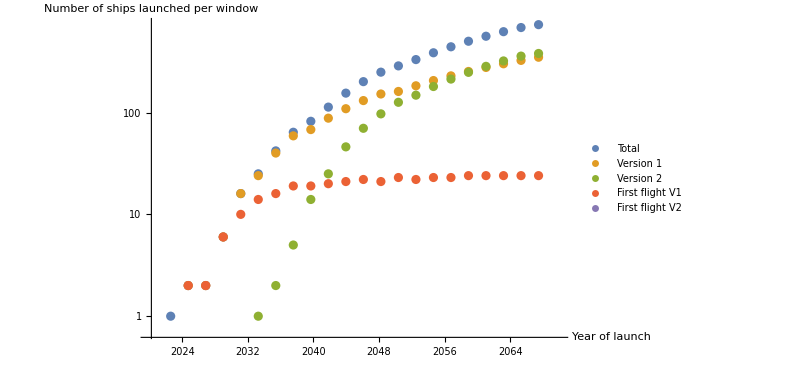

```mathematica
ListLogPlot[buildratedata,AxesStyle->16,AxesLabel->{"Year of launch","Number of ships \nlaunched per window"},ImageSize->600,PlotRange->{{2020,2070},All},PlotLegends->Placed[{"Total","Version 1", "Version 2","First flight V1","First flight V2"},Below]]
```

The target production rate for Version 1 and Version 2 is 20 hulls a window. At design cost of $500m/hull, the total expense is around $10b/window, which turns on at the start of production - full rate is achieved 6-10 years later. Thus program costs in construction begin at $4.5b/year in 2022, climb to $9b/year by 2032. Program costs in refitting equal construction costs by the mid 2040s, by which time passenger-derived revenue is (hopefully) supporting much of this burden.